## Integrals for the self-energy bubble in phi^3

```mathematica
Integrate[x(1-x),{x,0,1}]
```

1/6

```mathematica
Integrate[x(1-x),{x,0,1}]
```

1/6

```mathematica
Integrate[1-x(1-x),{x,0,1}]
```

5/6

```mathematica
4^(3/2)
```

8

```mathematica
PiFun[x_]:=1/12 ((3-Pi Sqrt[3])(-x) + (3-2Pi Sqrt[3])+2(-x) (1+4/(-x))^(3/2) ArcTanh[1/(1+4/(-x))^(1/2)])
```

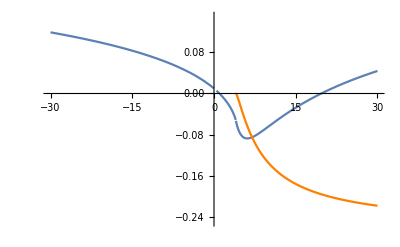

```mathematica
g1=Plot[{Re[PiFun[x]]/(-x+1)},{x,-30,30},PlotRange->{-0.25,0.15}];
g2=Plot[{Im[PiFun[x]]/(-x+1)},{x,4,30},PlotRange->{{0,30},{-0.3,0.1}},PlotStyle->{Orange}];
Show[g1,g2]
```

### Integrals that appear in the finite part

```mathematica
Integrate[x(1-x) Log[x(1-x)],{x,0,1}]
```

-5/18

```mathematica
1/12-1/2(Integrate[x(1-x) Log[x(1-x)],{x,0,1}]-Integrate[x(1-x) Log[1-x(1-x)],{x,0,1}])//Simplify
```

1/12 (-3+√3 π)

Same result as in Srednicki... OK.